```mathematica
(*холестерик*)
{ϵ1 = 1,ϵ2 = 1.2,q =10, L =1};
(*траектория, заряд. ЗДЕСЬ НЕОБОХОДИМО ВРУЧНУЮ ВВЕСТИ ТРАЕКТОРИЮ*)
x1[t_]:=0; x2[t_]:=0;z[t_]:=1t;
βp[t_]:=1/2 D[x1[t]+ⅈ x2[t],t];βm[t_]:=1/2 D[x1[t]-ⅈ x2[t],t];β3[t_]=D[z[t],t];Z=1;e=1;
```

```mathematica
GetPlaneProbability[s0_,kx0_,ky0_,kz0_]:=Module[{},
(*квантовые числа плосковолнового фотона*)
{s= s0,kx= kx0, ky= ky0,kz= kz0};

(*обозначения*)
ko=√(kx^2+ky^2+kz^2);
np=(√(kx^2+ky^2))/(√(kx^2+ky^2+kz^2));
ϕ=Arg[kx + ⅈ ky];
long ={k0= √ϵ2 ko,k3 =  √(ϵ2 ko^2-kp^2),Subscript[k, 3]=√(ko^2-kp^2), δϵ =(ϵ1 - ϵ2)/ϵ2, kp=np ko,n3= (√(ϵ2 ko^2-kp^2))/ko,Subscript[p, 3]= 2/π EllipticE[(-kp^2 δϵ)/((1+δϵ)k3^2)] √(1+δϵ)k3, χ1 = ϵ1-1, χ2 = ϵ2-1};
S[z_]:= q^-1 √((1+δϵ)k3^2)EllipticE[q z-ϕ,(-kp^2 δϵ)/((1+δϵ)k3^2)];
k32[z_]:=√((1+δϵ)k3^2+δϵ kp^2 Sin[q z-ϕ]^2);

(*модовые функции для квазиклассики vcb_ с учетом применимости теории (ведущий порядок по n_\perp)*)
(*обыкновенная волна*)
a1p[z_] := (k3/(2(k0^2-kp^2 Cos[(q z-ϕ)]^2)))^(1/2) ⅈ ⅇ^(ⅈ (q z-ϕ))ⅇ^(ⅈ k3 z) ;
a1m[z_] := (k3/(2(k0^2-kp^2 Cos[(q z-ϕ)]^2)))^(1/2)(-ⅈ) ⅇ^(-ⅈ  (q z-ϕ))ⅇ^(ⅈ k3 z) ;
a13[z_] := (kp Sin[ (q z-ϕ)] ⅇ^(ⅈ k3 z))/(√(2 k3((k0^2-kp^2 Cos[(q z-ϕ)]^2)))) ;
(* отраженная обычновенная волна*)
b1p[z_] := (k3/(2(k0^2-kp^2 Cos[(q z-ϕ)]^2)))^(1/2)ⅈ ⅇ^(ⅈ  (q z-ϕ))ⅇ^(-ⅈ k3 z) ;
b1m [z_]:= (k3/(2(k0^2-kp^2 Cos[(q z-ϕ)]^2)))^(1/2)(-ⅈ) ⅇ^(-ⅈ  (q z-ϕ))ⅇ^(-ⅈ k3 z) ;
b13[z_] := (-kp Sin[ (q z-ϕ)] ⅇ^(-ⅈ k3 z))/(√(2 k3((k0^2-kp^2 Cos[(q z-ϕ)]^2)))) ;
(*необыкновенная волна*)
ζ[z_]:=k3^2 Cos[q z -ϕ]-ⅈ k0^2 Sin[q z -ϕ];
ζc[z_]:=k3^2 Cos[q z -ϕ]+ⅈ k0^2 Sin[q z -ϕ];
a2p[z_] := (2k32[z] k0^2(k0^2-kp^2 Cos[(q z-ϕ)]^2))^(-1/2)ζc[z] ⅇ^(ⅈ S[z]);
a2m[z_] :=  (2k32[z] k0^2(k0^2-kp^2 Cos[(q z-ϕ)]^2))^(-1/2)ζ[z] ⅇ^(ⅈ S[z]);
a23[z_] := -kp Cos[ (q z-ϕ)] (k32[z]/(2 k0^2(k0^2-kp^2 Cos[q z-ϕ]^2)))^(1/2)ⅇ^(ⅈ S[z]) ;
(*необыкновенная отраженная волна*)
b2p[z_] := (2k32[z] k0^2(k0^2-kp^2 Cos[(q z-ϕ)]^2))^(-1/2)ζc[z] ⅇ^(-ⅈ S[z]);
b2m[z_] :=  (2k32[z] k0^2(k0^2-kp^2 Cos[(q z-ϕ)]^2))^(-1/2)ζ[z] ⅇ^(-ⅈ S[z]);
b23[z_] :=kp Cos[ (q z-ϕ)] (k32[z]/(2 k0^2(k0^2-kp^2 Cos[q z-ϕ]^2)))^(1/2)ⅇ^(-ⅈ S[z]) ;
K = ({{1+kp^2/(2 (k0^2-kp^2)), kp^2/(2 (k0^2-kp^2))}, {kp^2/(2 (k0^2-kp^2)), 1+kp^2/(2 (k0^2-kp^2))}});

u11[z_] := ({{a1p[z], a2p[z]}, {a1m[z], a2m[z]}});
u12[z_]:= ({{b1p[z], b2p[z]}, {b1m[z], b2m[z]}});
u21[z_]:= -ⅈ K. u11'[z];
u22[z_]:= -ⅈ K. u12'[z];
U=({{u11[0][[1,1]], u11[0][[1,2]], u12[0][[1,1]], u12[0][[1,2]]}, {u11[0][[2,1]], u11[0][[2,2]], u12[0][[2,1]], u12[0][[2,2]]}, {u21[0][[1,1]], u21[0][[1,2]], u22[0][[1,1]], u22[0][[1,2]]}, {u21[0][[2,1]], u21[0][[2,2]], u22[0][[2,1]], u22[0][[2,2]]}});

gT =1/(√2) ({{√(1-np^2) -s, √(1-np^2)+s, ko(1-s √(1-np^2)), ko(1+s √(1-np^2))}});
{r1,r2,l1,l2} =LinearSolve[U,gTᵀ];
(*сборка волновой функции*)
ψp[x1_,x2_,z_] =( r1 a1p[z]+l1 b1p[z]+r2 a2p[z]+l2 b2p[z])ⅇ^(ⅈ ϕ)ⅇ^(ⅈ (kx x1+ky x2));
ψm[x1_,x2_,z_] = (r1 a1m[z]+l1 b1m[z]+r2 a2m[z]+l2 b2m[z] )ⅇ^(-ⅈ ϕ)ⅇ^(ⅈ (kx x1+ky x2));
ψ3[x1_,x2_,z_] =ⅈ kp/(2(k0^2-kp^2))D[ψp[x1,x2,z] ⅇ^(-ⅈ ϕ)+ψm[x1,x2,z] ⅇ^(ⅈ ϕ),z];
(*******нормировочный множитель******************)
H = 1/(√2)({{√(1-np^2)-1, √(1-np^2)+1, -√(1-np^2)-1, -√(1-np^2)+1}, {√(1-np^2)+1, √(1-np^2)-1, -√(1-np^2)+1, -√(1-np^2)-1}, {ko(1-√(1-np^2)), ko(1+√(1-np^2)), ko(1+√(1-np^2)), ko(1-√(1-np^2))}, {ko(1+√(1-np^2)), ko(1-√(1-np^2)), ko(1-√(1-np^2)), ko(1+√(1-np^2))}});
T = DiagonalMatrix[{ⅇ^(-ⅈ k3 L),ⅇ^(-ⅈ Subscript[p, 3] L),ⅇ^(ⅈ k3 L),ⅇ^(ⅈ Subscript[p, 3] L)}];
T2 =DiagonalMatrix[{ⅇ^(-ⅈ Subscript[k, 3] L),ⅇ^(-ⅈ Subscript[k, 3] L),ⅇ^(ⅈ Subscript[k, 3] L),ⅇ^(ⅈ Subscript[k, 3] L)}];
al=Inverse[T2].Inverse[H].U.T.Inverse[U].gTᵀ;
norm = Abs[2(1+Conjugate[alᵀ].al)^-1];
(*амплитуда*)
ampl = NIntegrate[βp[t] ψp[x1[t],x2[t],z[t]] + βm[t] ψm[x1[t],x2[t],z[t]] + β3[t] ψ3[x1[t],x2[t],z[t]],{t,0,L/β3[0]}];
(*вероятность*)
dP=Z^2 e^2 Abs[ampl]^2 norm/(2ko 2^3 π^3);
dP

]
```

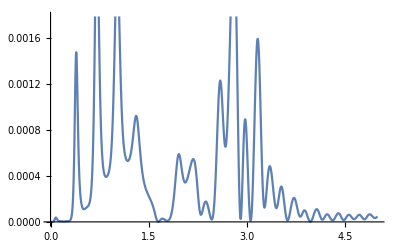

```mathematica
Plot[GetPlaneProbability[1,1,1,t],{t,0,5}]
```

```mathematica
GetPlaneProbability[1,1,1,5]//Timing
```

{0.15625,{{3.43231×10^-7}}}